# Cleaning Up Yorkeys Knob Dataset

## Functions

```mathematica
Themes`AddThemeRules["GridPoints"
,AspectRatio->1
,DefaultPlotStyle->Thread@Directive[{Purple,Blue,Red},PointSize[.005],Opacity[.4]]
,Frame->True
,FrameStyle->Directive[Gray,Thick]
,GridLines->Automatic
,GridLinesStyle->Directive[Opacity[.5],LightGray]
]
```

GridPoints

## Data

```mathematica
SetDirectory["/Volumes/marshallShare/MGDrivE_Datasets/ThresholdDependent/"];
```

Yorkeys

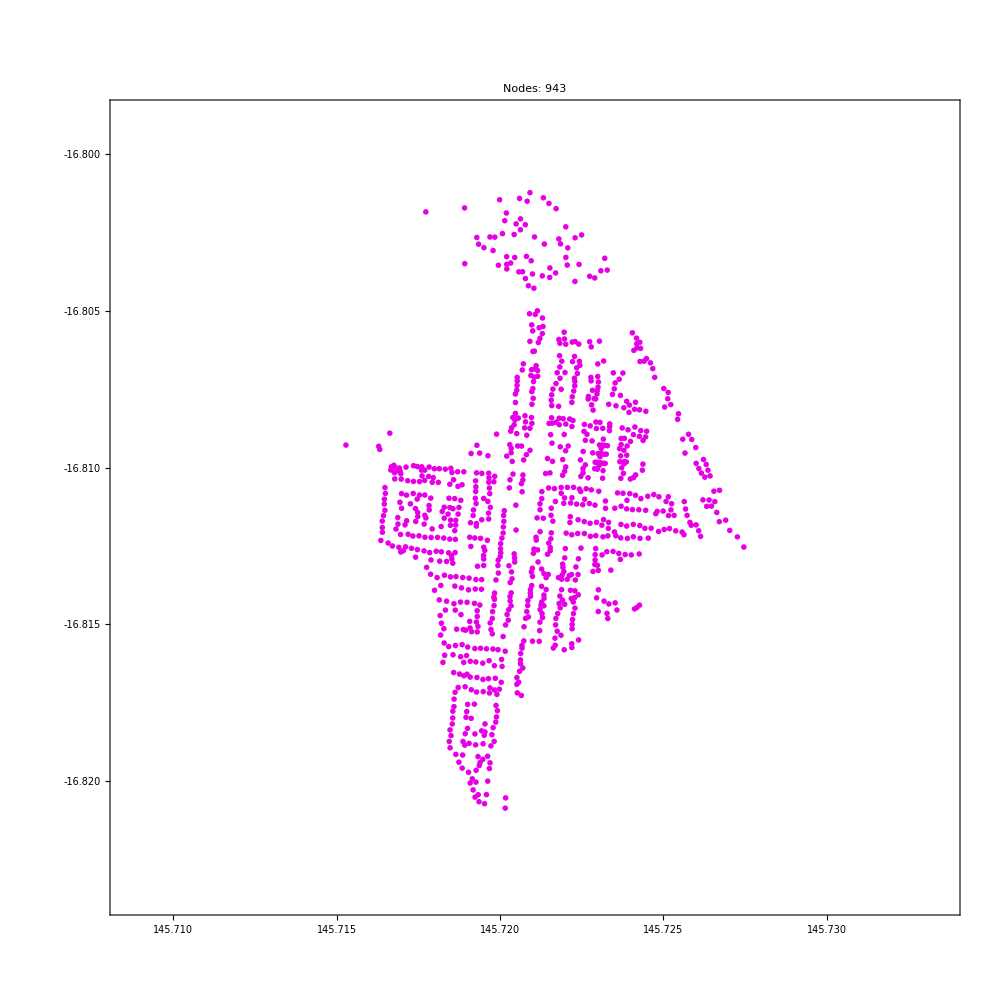

```mathematica
{folder,locationTag}={"./GeoLocations","YorkeysKnob_02"};
rawData=Import[folder<>"/Original/"<>locationTag<>".csv"];
clustered=FindClusters[rawData//Sort,2];
ListPlot[clustered[[2]]
,AspectRatio->1
,GridLines->None
,ImageSize->1000
,PlotLabel->("Nodes: "<>ToString[Length[rawData]])
,PlotRange->({#-.0125,#+.0125}&/@(Mean/@Transpose[clustered[[2]]]))
,PlotStyle->Directive[{Darker[Magenta,.1],PointSize[.1]}]
,PlotTheme->"Business"
]
(*Export[folder<>"/Curated/images/"<>locationTag<>".jpg",%,ImageResolution->500]*)
(*Export[folder<>"/Curated/"<>locationTag<>".csv",clustered[[2]]]*)
```

Yorkeys and Trinity

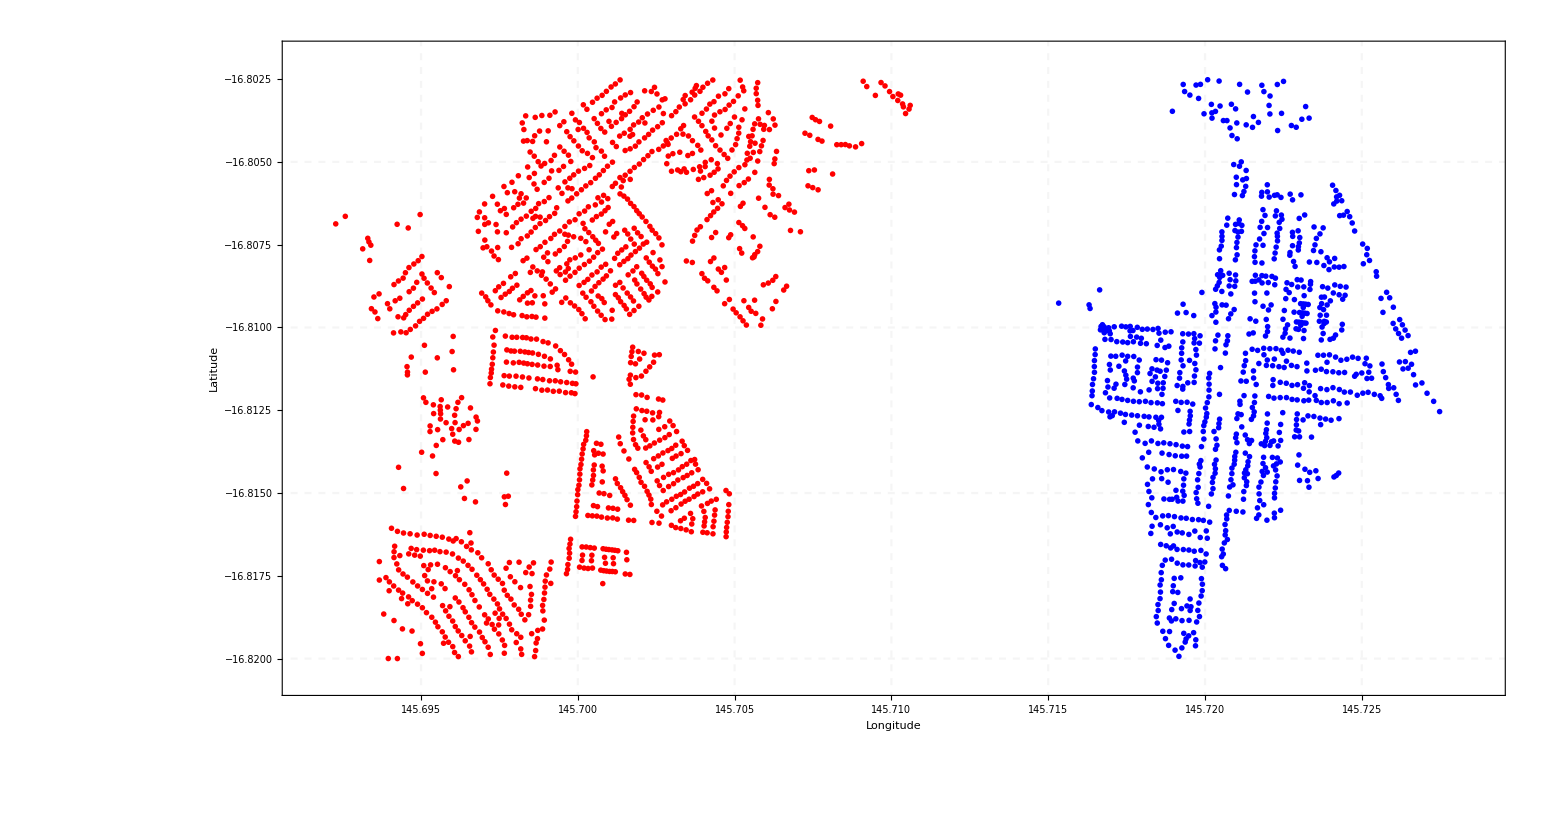

./GeoLocations/Curated/images/YorkeysKnob_01.pdf

```mathematica
{folder,locationTag}={"./GeoLocations","YorkeysKnob_01"};
rawData=Import[folder<>"/Original/"<>locationTag<>".csv"][[2;;All]];
filteredData=Cases[rawData//Sort,{a_,b_}/;(a>145.775||-16.82<b<-16.8025)];
clusteredData=FindClusters[filteredData,2];
houses=ListPlot[clusteredData
,AspectRatio->.525
,Frame->True
,FrameLabel->(Style[#,75]&/@{"Longitude","Latitude"})
,FrameStyle->Thick
,FrameTicks->Automatic
,FrameTicksStyle->30
,GridLines->Automatic
,GridLinesStyle->Directive[Dashed,Thickness[.001],Opacity[.25]]
,ImageSize->1750
(*,PlotLabel->("Nodes: "<>ToString[Length[rawData]])*)
,PlotStyle->{Red,Blue}
,PlotRange->{{145.7088243937645-.0175,145.7088243937645+.02},{-16.810732755236703-.010,-16.810732755236703+.009}}
,PlotTheme->"Business"
]
Export[folder<>"/Curated/images/"<>locationTag<>".pdf",%,ImageSize->1750,ImageResolution->600]
(*Export[folder<>"/Curated/"<>locationTag<>".csv",clusteredData//Flatten[#,1]&]*)
```

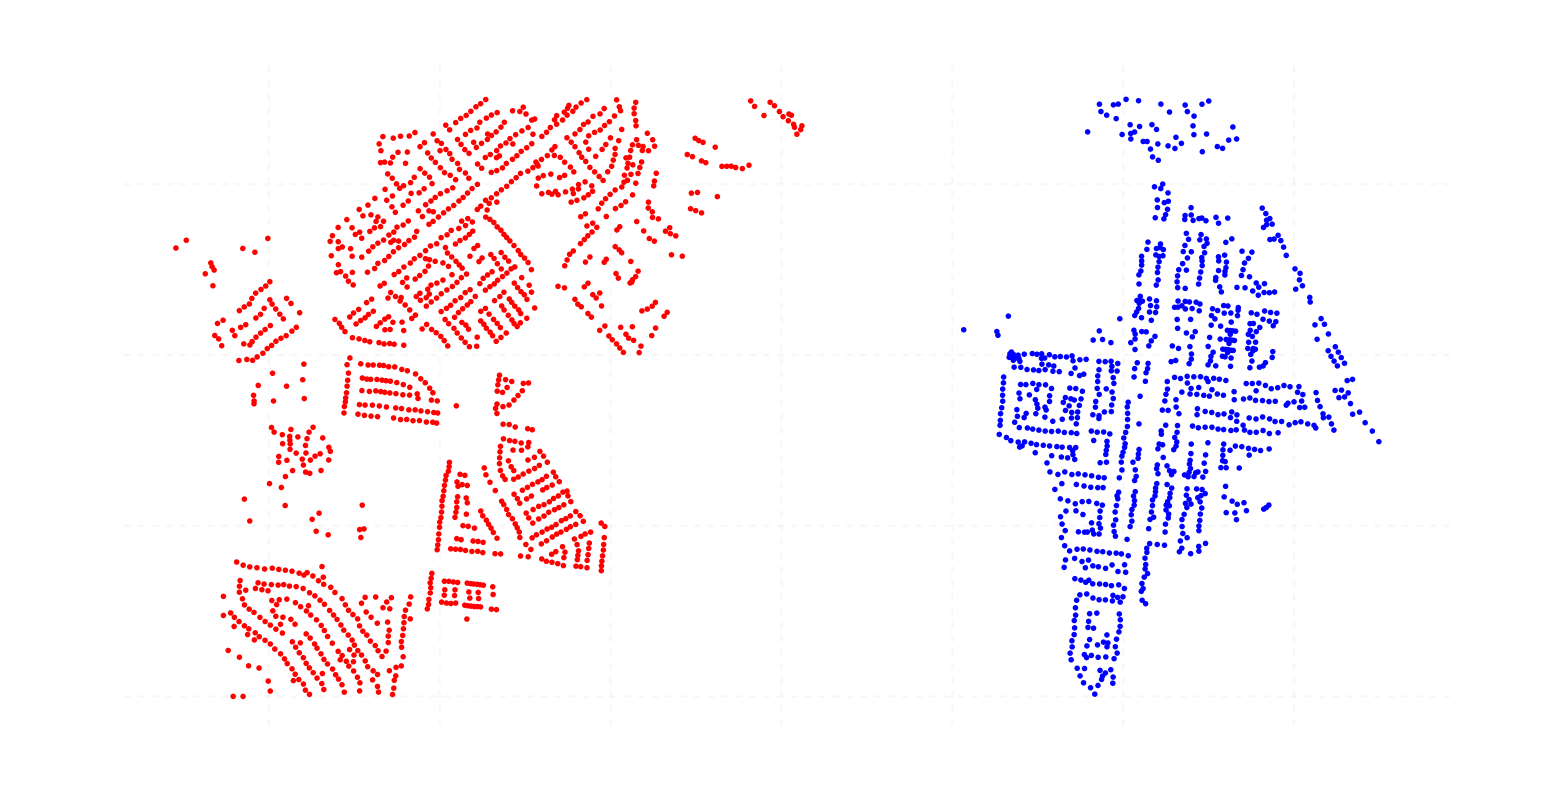

./GeoLocations/Curated/images/YorkeysKnob_01Clean.png

```mathematica
clusteredData=FindClusters[filteredData,2];
housesC=ListPlot[clusteredData
,AspectRatio->Automatic
,Axes->False
,Frame->None
,FrameLabel->None
,FrameStyle->Thick
,FrameTicks->None
,FrameTicksStyle->30
,GridLines->Automatic
,GridLinesStyle->Directive[Dashed,Thickness[.001],Opacity[.2]]
,ImageSize->1750
(*,PlotLabel->("Nodes: "<>ToString[Length[rawData]])*)
,PlotStyle->(Directive[Opacity[1],#,PointSize[.1]]&/@{Red,Blue})
,PlotRange->{{145.7088243937645-.0175,145.7088243937645+.02},{-16.810732755236703-.010,-16.810732755236703+.009}}
,PlotTheme->"Business"
]
Export[folder<>"/Curated/images/"<>locationTag<>"Clean.png",%,ImageSize->4000]
```

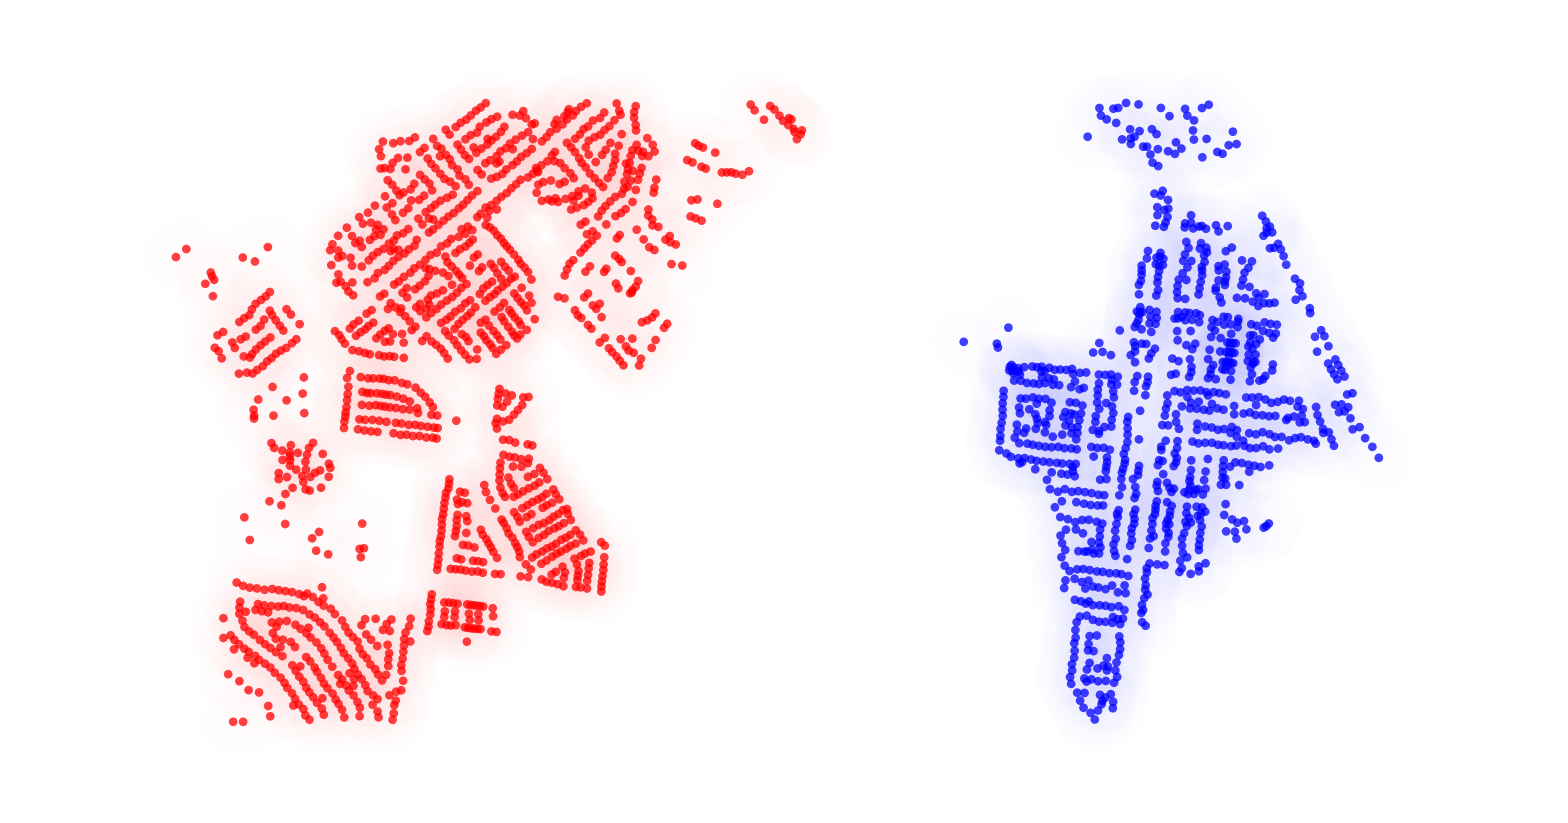

./GeoLocations/Curated/images/YorkeysKnob_01Clean.png

```mathematica
housesB=ListPlot[clusteredData
,AspectRatio->.525
,Axes->False
,Frame->None
,FrameLabel->None
,FrameStyle->Thick
,FrameTicks->None
,FrameTicksStyle->30
,GridLines->None
,GridLinesStyle->Directive[Dashed,Thickness[.001],Opacity[.25]]
,ImageSize->1750
(*,PlotLabel->("Nodes: "<>ToString[Length[rawData]])*)
,PlotStyle->{Directive[Red,Opacity[.75],PointSize[.004]],Directive[Blue,Opacity[.75],PointSize[.004]]}
,PlotRange->{{145.7088243937645-.0175,145.7088243937645+.02},{-16.810732755236703-.010,-16.810732755236703+.009}}
];
housesC=ListPlot[clusteredData
,AspectRatio->.525
,Axes->False
,Frame->None
,FrameLabel->None
,FrameStyle->Thick
,FrameTicks->None
,FrameTicksStyle->30
,GridLines->None
,GridLinesStyle->Directive[Dashed,Thickness[.001],Opacity[.25]]
,ImageSize->1750
(*,PlotLabel->("Nodes: "<>ToString[Length[rawData]])*)
,PlotStyle->{Directive[Red,Opacity[.003],PointSize[.05]],Directive[Blue,Opacity[.003],PointSize[.05]]}
,PlotRange->{{145.7088243937645-.0175,145.7088243937645+.02},{-16.810732755236703-.010,-16.810732755236703+.009}}
];
Show[housesC,housesB]
Export[folder<>"/Curated/images/"<>locationTag<>"Clean.png",%,ImageSize->4000]
```

```mathematica
features=GeoGraphics[GeoRange->{{-16.810732755236703-.010,-16.810732755236703+.009},{145.7088243937645-.0175,145.7088243937645+.02}},GeoRangePadding->Quantity[100,"Meters"],GeoBackground->GeoStyling["StreetMapNoLabels"]];
Show[features,houses]
Export[folder<>"/Curated/images/"<>locationTag<>"Features.pdf",%,ImageSize->1750,ImageResolution->600]
```

-Graphics-

./GeoLocations/Curated/images/YorkeysKnob_01Features.pdf

Trinity

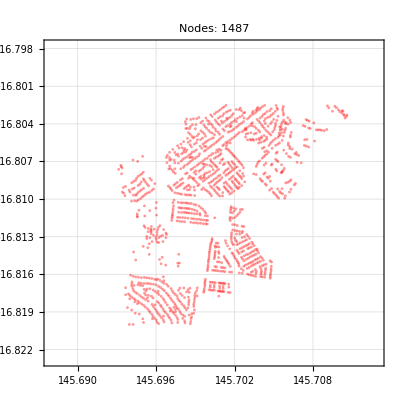

./GeoLocations/Curated/images/YorkeysKnob_03.jpg

./GeoLocations/Curated/YorkeysKnob_03.csv

```mathematica
{folder,locationTag}={"./GeoLocations","YorkeysKnob_03"};
rawData=Import[folder<>"/Original/"<>locationTag<>".csv"][[2;;All]];
filteredData=Cases[rawData//Sort,{a_,b_}/;(a>145.775||-16.82<b<-16.8025)];
ListPlot[filteredData
,PlotLabel->("Nodes: "<>ToString[Length[rawData]])
,PlotStyle->Red
,PlotTheme->"GridPoints"
,PlotRange->({#-.0125,#+.0125}&/@(Mean/@Transpose[filteredData]))
]
Export[folder<>"/Curated/images/"<>locationTag<>".jpg",%,ImageResolution->500]
(*Export[folder<>"/Curated/"<>locationTag<>".csv",filteredData]*)
```

Gordonvale

```mathematica
dsk=Graphics[{EdgeForm[Directive[hexToRGB["#141759"],Opacity[.05],Thickness[.3]]],hexToRGB["#141759"],Disk[{0,0},.2]}];
{folder,locationTag}={"./GeoLocations","YorkeysKnob_02"};
rawData=Import[folder<>"/Original/"<>locationTag<>".csv"][[2;;All]];
plot=ListPlot[rawData
,AspectRatio->1
,Axes->False
,Frame->False
,FrameLabel->None(*(Style[#,75]&/@{"Longitude","Latitude"})*)
(*,FrameTicksStyle->30*)
,ImageSize->1750
(*,PlotLabel->("Nodes: "<>ToString[Length[rawData]])*)
,PlotMarkers->{dsk,.015}
,PlotStyle->Directive[{Darker[Magenta,0],Opacity[.025]}]
,PlotRange->({#-.0105,#+.0105}&/@(Mean/@Transpose[rawData]))(*({#-.0325,#+.0325}&/@(Mean/@Transpose[rawData]))*)
];
(*Export[folder<>"/Curated/images/"<>locationTag<>".jpg",plot,ImageResolution->500]*)
Export[folder<>"/Curated/images/"<>locationTag<>".pdf",plot,ImageResolution->500]
```

./GeoLocations/Curated/images/YorkeysKnob_02.pdf

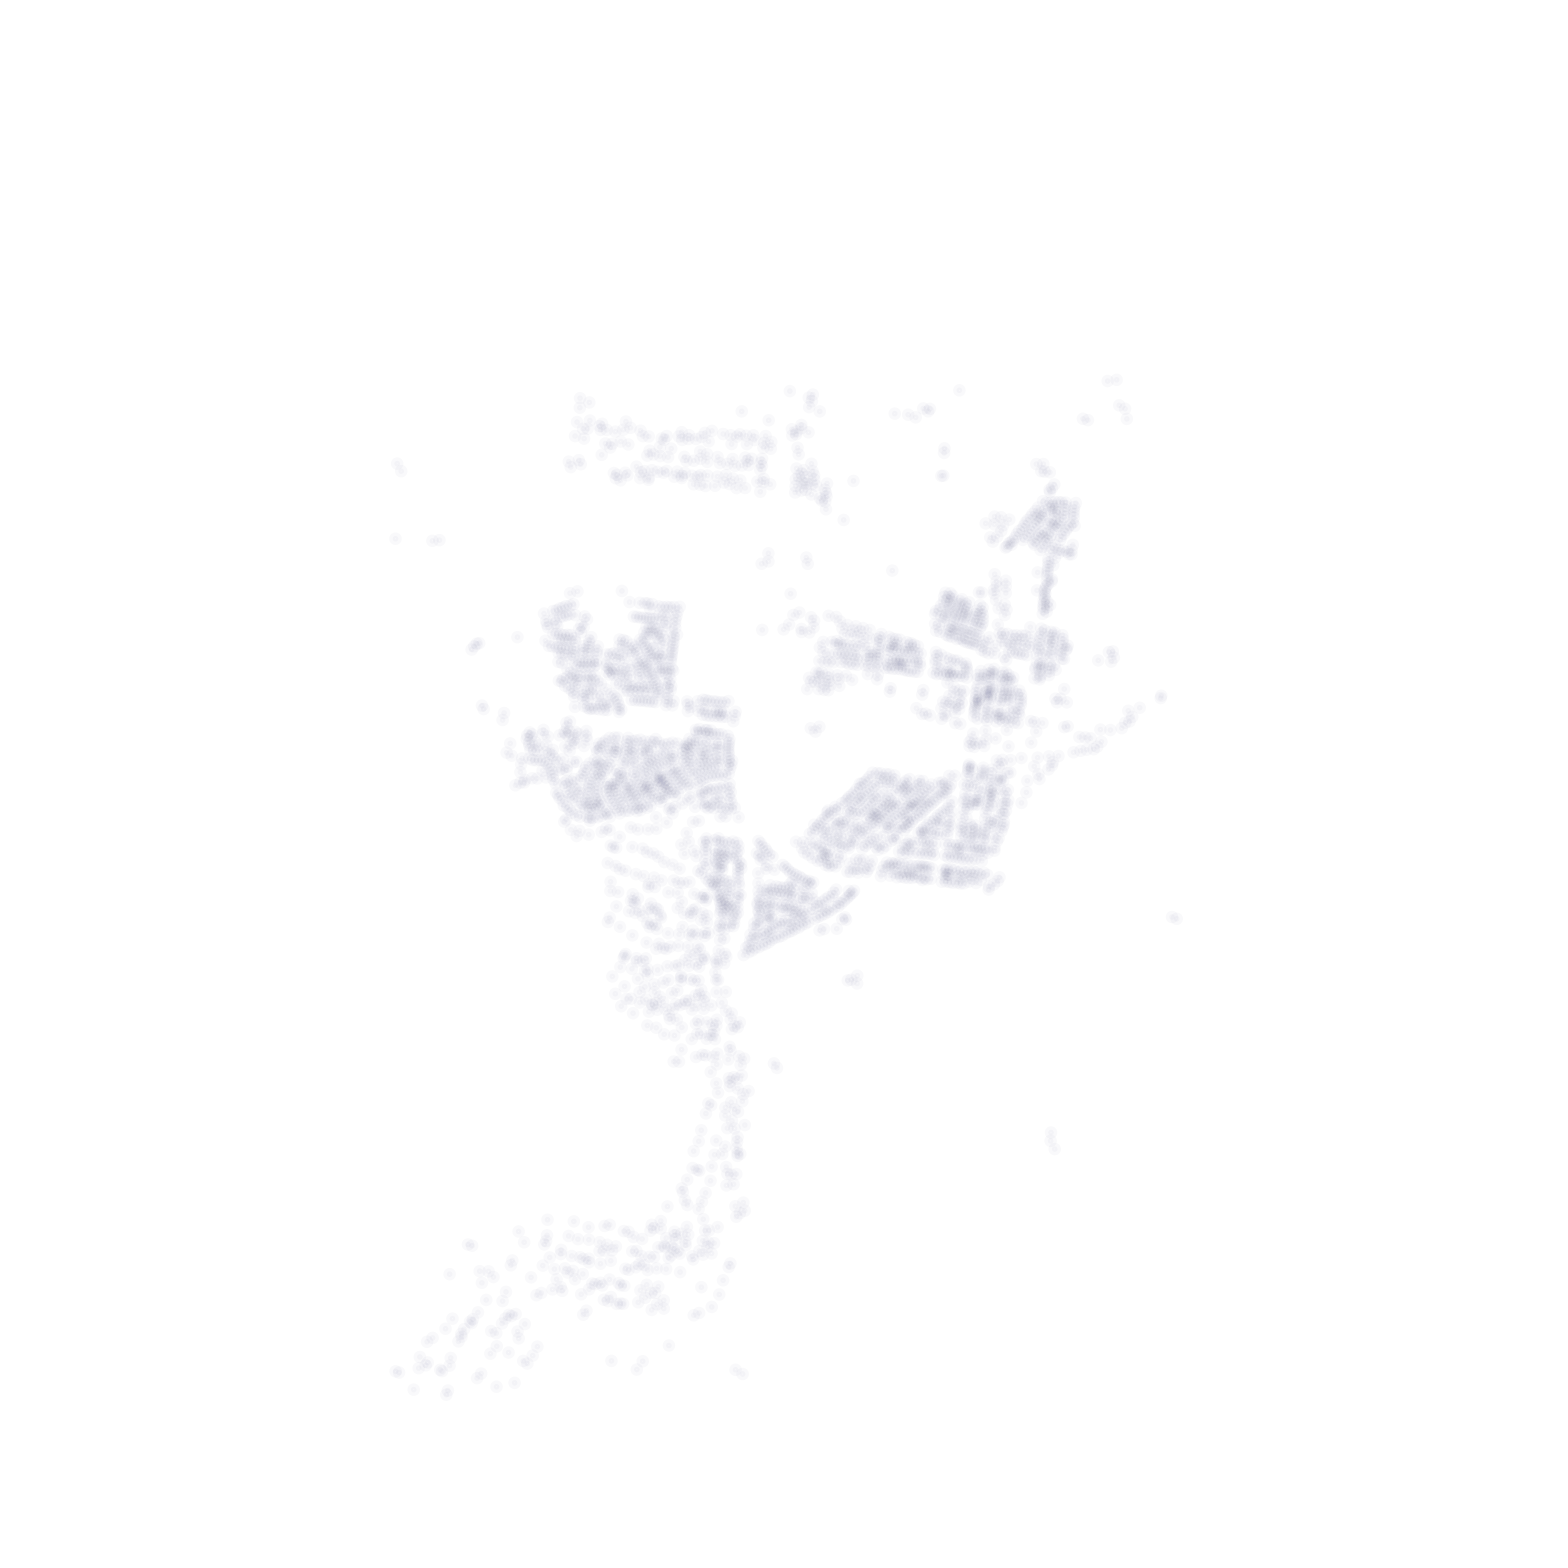

./GeoLocations/Curated/images/Gordonvale_01.pdf

```mathematica
dsk=Graphics[{EdgeForm[Directive[hexToRGB["#141759"],Opacity[.05],Thickness[.3]]],hexToRGB["#141759"],Disk[{0,0},.2]}];
{folder,locationTag}={"./GeoLocations","Gordonvale_01"};
rawData=Import[folder<>"/Original/"<>locationTag<>".csv"][[2;;All]];
plot=ListPlot[rawData
,AspectRatio->1
,Axes->False
,Frame->False
,FrameLabel->None(*(Style[#,75]&/@{"Longitude","Latitude"})*)
(*,FrameTicksStyle->30*)
,ImageSize->1750
(*,PlotLabel->("Nodes: "<>ToString[Length[rawData]])*)
,PlotMarkers->{dsk,.0075}
,PlotStyle->Directive[{Darker[Magenta,0],Opacity[.025]}]
,PlotRange->({#-.0325,#+.0325}&/@(Mean/@Transpose[rawData]))
]
(*Export[folder<>"/Curated/images/"<>locationTag<>".jpg",plot,ImageResolution->500]*)
Export[folder<>"/Curated/images/"<>locationTag<>".pdf",plot,ImageResolution->500]
```